```mathematica
Clear["Global`*"]
```

## BDH Exercises

Set up system and Jacobian

```mathematica
system = {
x(1-x)-x*y,
y(1-y)+x*y-y*z,
z(1-z)+y*z
}
```

{(1-x) x-x y,x y+(1-y) y-y z,y z+(1-z) z}

```mathematica
vars={x,y,z}
```

{x,y,z}

```mathematica
jacobian=D[system,{vars}]
```

{{1-2 x-y,-x,0},{y,1+x-2 y-z,-y},{0,z,1+y-2 z}}

```mathematica
jacobian//TraditionalForm
```

(-2 x-y+1 | -x | 0
y | x-2 y-z+1 | -y
0 | z | y-2 z+1)

```mathematica
equilibria={
{x->1,y->0,z->0},
{x->0,y->1,z->0},
{x->0,y->0,z->1},
{x->1,y->0,z->1}
}
```

{{x→1,y→0,z→0},{x→0,y→1,z→0},{x→0,y→0,z→1},{x→1,y→0,z→1}}

-Graphics3D-

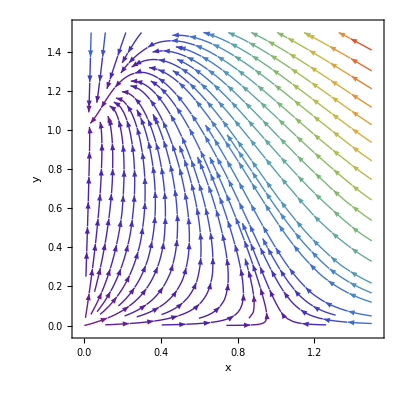

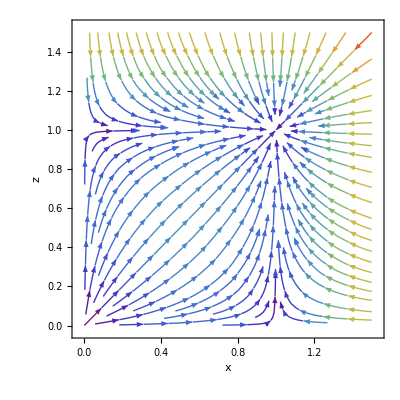

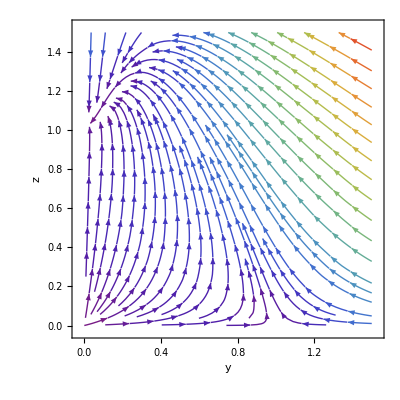

```mathematica
VectorPlot3D[
{system},
{x,0.0,1.5},
{y,0.0,1.5},
{z,0.0,1.5},
Axes->True,
AxesLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},
VectorColorFunction->"Rainbow",
VectorPoints->6,
VectorScale->{0.1,.7,None}
]
StreamPlot[{x(1-x)-x*y,y(1-y)+x*y-y*0},{x,0.0,1.5},{y,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24]},
Frame->True,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{x(1-x)-x*0,z(1-z)+0*z},{x,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{y(1-y)+0*y-y*z,z(1-z)+y*z},{y,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,StreamColorFunction->"Rainbow",PlotRangePadding->None]
```

### Calculating the eigenvalues of the equilibrium of coexistence

```mathematica
coexistence=(Solve[{system==0,x≠0,y≠0,z≠0},{x,y,z}])
```

{{x→2/3,y→1/3,z→4/3}}

```mathematica
Eigenvalues[D[system,{vars}]/.coexistence]
```

{-1,-2/3+(2 ⅈ)/3,-2/3-(2 ⅈ)/3}

### Top Predator Disease State

```mathematica
dsys={
x(1-x)-x*y,
y(1-y)+x*y-y*z,
z(1-z)+y*z-γ*z
}
```

{(1-x) x-x y,x y+(1-y) y-y z,y z+(1-z) z-z γ}

```mathematica
zeros={0,0,0}
```

{0,0,0}

```mathematica
dsolns=Solve[dsys==zeros,vars]
```

{{x→0,y→0,z→1-γ},{x→0,y→1,z→0},{x→0,y→γ/2,z→(2-γ)/2},{x→1,y→0,z→0},{x→1,y→0,z→1-γ},{x→(2-γ)/3,y→(1+γ)/3,z→-2/3 (-2+γ)},{x→0,y→0,z→0}}

```mathematica
eoc=dsolns[[6]]
```

{x→(2-γ)/3,y→(1+γ)/3,z→-2/3 (-2+γ)}

```mathematica
eqpoint={x,y,z}/.eoc
```

{(2-γ)/3,(1+γ)/3,-2/3 (-2+γ)}

```mathematica
D[eqpoint,γ]
```

{-1/3,1/3,-2/3}

```mathematica
Manipulate[VectorPlot3D[{x(1-x)-x*y,y(1-y)+x*y-y*z,z(1-z)+y*z-γ*z},{x,0,1},{y,0,1},{z,0,1}],{γ,0,1}]
```

```mathematica
djac=D[dsys,{vars}]/.eoc
```

{{1+1/3 (-1-γ)-(2 (2-γ))/3,1/3 (-2+γ),0},{(1+γ)/3,1+(2-γ)/3+2/3 (-2+γ)-(2 (1+γ))/3,1/3 (-1-γ)},{0,-2/3 (-2+γ),1+4/3 (-2+γ)-γ+(1+γ)/3}}

```mathematica
djac//TraditionalForm
```

(1/3 (-γ-1)-(2 (2-γ))/3+1 | (γ-2)/3 | 0
(γ+1)/3 | (2-γ)/3+(2 (γ-2))/3-(2 (γ+1))/3+1 | 1/3 (-γ-1)
0 | -2/3 (γ-2) | (4 (γ-2))/3-γ+(γ+1)/3+1)

```mathematica
eqpoint//TraditionalForm
```

{(2-γ)/3,(γ+1)/3,-2/3 (γ-2)}

```mathematica
Reduce[eqpoint>0,γ]
```

-1<γ<2

## Equilibria Point Evaluation

### First equilibrium point (1,0,0)

Find the eigenvalues and eigenvectors associated with the point

```mathematica
jone=jacobian/.equilibria[[1]]
```

{{-1,-1,0},{0,2,0},{0,0,1}}

```mathematica
Eigensystem[jone]
```

{{2,-1,1},{{-1,3,0},{1,0,0},{0,0,1}}}

```mathematica
sysone=jone.(vars-(vars/.equilibria[[1]]))
```

{1-x-y,2 y,z}

Three dimensional vector plot of the linearized system about the point

```mathematica
VectorPlot3D[
{sysone},
{x,0.0,1.2},
{y,0.0,1.2},
{z,0.0,1.2},
Axes->True,
AxesLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},
VectorColorFunction->"Rainbow",
VectorPoints->5,
VectorScale->{0.1,.7,None},
PerformanceGoal->"Quality",
ImageSize->Full
]
```

-Graphics3D-

Two Dimensional “slices” along each of the center planes.

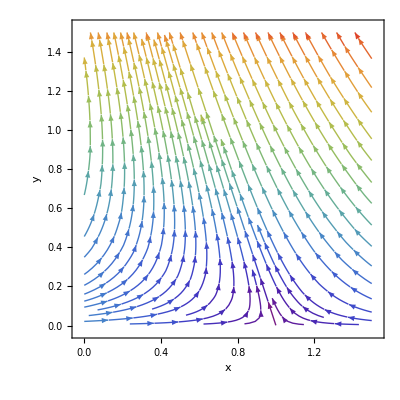

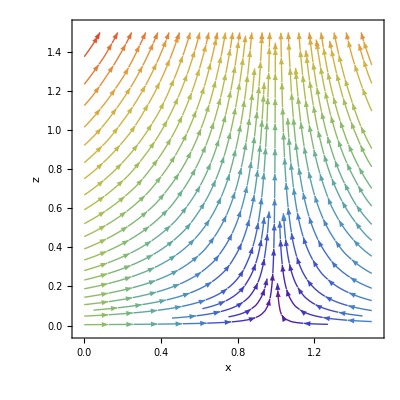

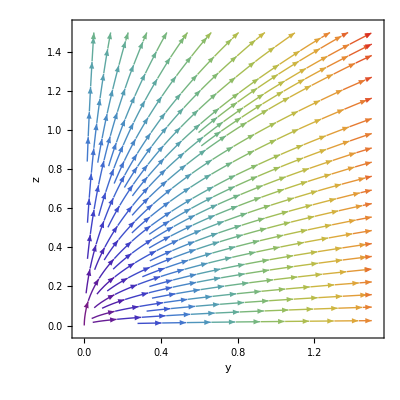

```mathematica
StreamPlot[{1-x-y,2y},{x,0.0,1.5},{y,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24]},
Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{1-x,z},{x,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{2y,z},{y,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
```

### Second equilibrium point (0,1,0)

```mathematica
equilibria[[2]]
```

{x→0,y→1,z→0}

```mathematica
jtwo=jacobian/.equilibria[[2]]
```

{{0,0,0},{1,-1,-1},{0,0,2}}

```mathematica
Eigensystem[jtwo]
```

{{2,-1,0},{{0,-1,3},{0,1,0},{1,1,0}}}

```mathematica
(vars-(vars/.equilibria[[2]]))
```

{x,-1+y,z}

```mathematica
systwo=jtwo.(vars-(vars/.equilibria[[2]]))
```

{0,1+x-y-z,2 z}

```mathematica
Reduce[systwo[[2]]>0,{x}]
```

(y|z)∈ℝ&&x>-1+y+z

-Graphics3D-

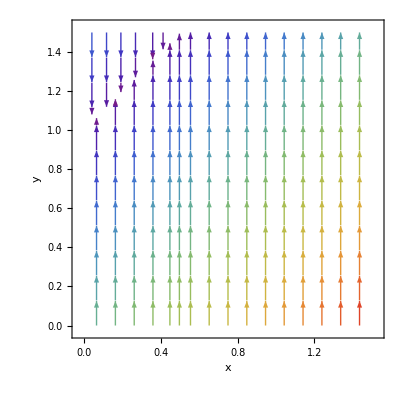

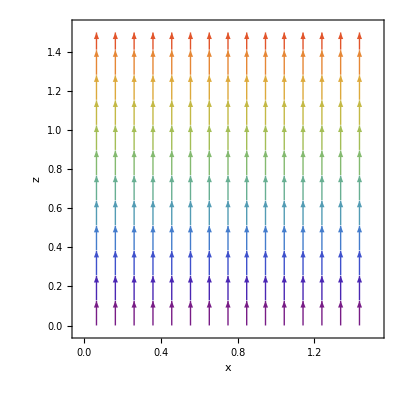

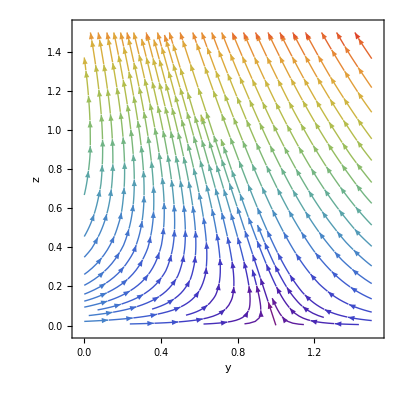

```mathematica
VectorPlot3D[
{systwo},
{x,0.0,1.2},
{y,0.0,1.2},
{z,0.0,1.2},
Axes->True,
AxesLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},
VectorColorFunction->"Rainbow",
VectorPoints->5,
VectorScale->{0.1,.7,None},
PerformanceGoal->"Quality",
ImageSize->Full
]
StreamPlot[{0,1+x-y},{x,0.0,1.5},{y,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24]},
Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{0,2z},{x,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{1-y-z,2z},{y,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
```

### Third equilibrium point (0,0,1)

```mathematica
equilibria[[3]]
```

{x→0,y→0,z→1}

```mathematica
jthree=jacobian/.equilibria[[3]]
```

{{1,0,0},{0,0,0},{0,1,-1}}

```mathematica
Eigensystem[jthree]
```

{{-1,1,0},{{0,0,1},{1,0,0},{0,1,1}}}

```mathematica
systhree=jthree.(vars-(vars/.equilibria[[3]]))
```

{x,0,1+y-z}

-Graphics3D-

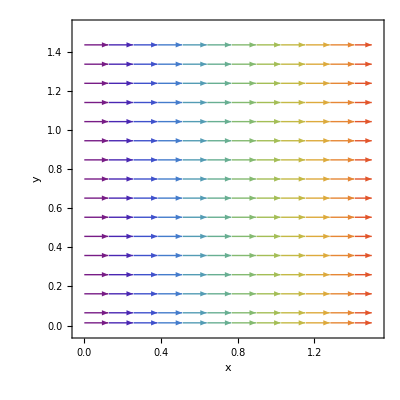

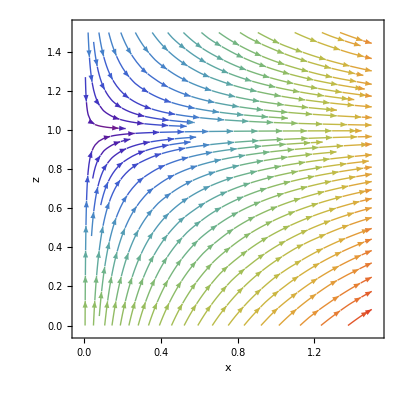

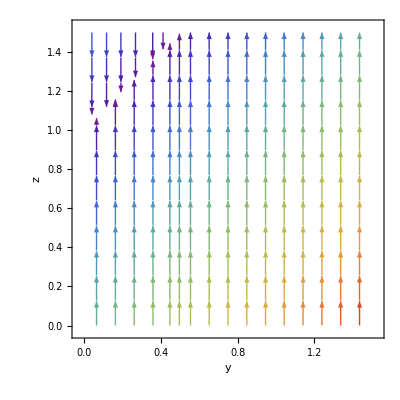

```mathematica
VectorPlot3D[
{systhree},
{x,0.0,1.2},
{y,0.0,1.2},
{z,0.0,1.2},
Axes->True,
AxesLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},
VectorColorFunction->"Rainbow",
VectorPoints->5,
VectorScale->{0.1,.7,None},
PerformanceGoal->"Quality",
ImageSize->Full
]
StreamPlot[{x,0},{x,0.0,1.5},{y,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24]},
Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{x,1-z},{x,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{0,1+y-z},{y,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
```

### Fourth equilibrium point (1,0,1)

```mathematica
equilibria[[4]]
```

{x→1,y→0,z→1}

```mathematica
jfour=jacobian/.equilibria[[4]]
```

{{-1,-1,0},{0,1,0},{0,1,-1}}

```mathematica
Eigensystem[jfour]
```

{{-1,-1,1},{{0,0,1},{1,0,0},{-1,2,1}}}

```mathematica
sysfour=jfour.(vars-(vars/.equilibria[[4]]))
```

{1-x-y,y,1+y-z}

-Graphics3D-

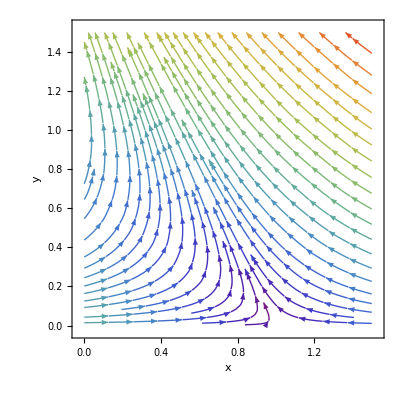

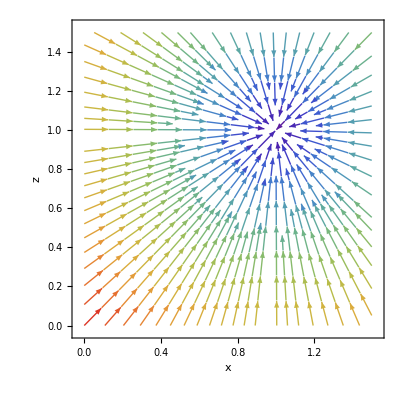

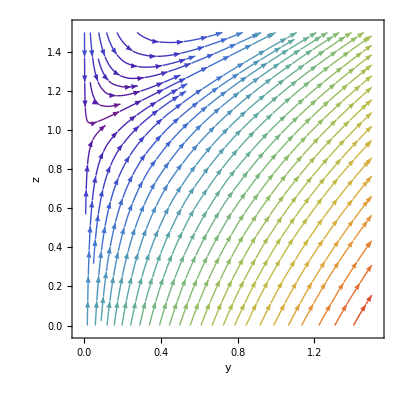

```mathematica
VectorPlot3D[
{sysfour},
{x,0.0,1.2},
{y,0.0,1.2},
{z,0.0,1.2},
Axes->True,
AxesLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},
VectorColorFunction->"Rainbow",
VectorPoints->5,
VectorScale->{0.1,.7,None},
PerformanceGoal->"Quality",
ImageSize->Full
]
StreamPlot[{1-x-y,y},{x,0.0,1.5},{y,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["y",Bold,FontSize->24]},
Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{1-x,1-z},{x,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["x",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
StreamPlot[{y,1+y-z},{y,0.0,1.5},{z,0.0,1.5},FrameLabel->{
Style["y",Bold,FontSize->24],Style["z",Bold,FontSize->24]},Frame->True,ImageSize->Full,StreamColorFunction->"Rainbow",PlotRangePadding->None]
```

```mathematica
jacobian
```

{{1-2 x-y,-x,0},{y,1+x-2 y-z,-y},{0,z,1+y-2 z}}

```mathematica
equilibria[[2]]
```

{x→0,y→1,z→0}

```mathematica
jacobian/.equilibria[[2]]
```

{{0,0,0},{1,-1,-1},{0,0,2}}

## Problem 6 - Moose Disease Model

```mathematica
system = {
dx=x(1-x)-x*y,
dy=y(1-y)+x*y-y*z-β*y,
dz=z(1-z)+y*z
}
```

{(1-x) x-x y,x y+(1-y) y-y z-y β,y z+(1-z) z}

```mathematica
vars={x,y,z};
```

```mathematica
jacobian=D[system,{vars}]
```

{{1-2 x-y,-x,0},{y,1+x-2 y-z-β,-y},{0,z,1+y-2 z}}

```mathematica
equilibria = Solve[system == 0,vars]
```

{{x→0,y→0,z→1},{x→0,y→1-β,z→0},{x→0,y→-β/2,z→(2-β)/2},{x→1,y→0,z→0},{x→1,y→0,z→1},{x→β/2,y→(2-β)/2,z→0},{x→(2+β)/3,y→(1-β)/3,z→(4-β)/3},{x→0,y→0,z→0}}

```mathematica
nonzeroequil = equilibria[[7]]
```

{x→(2+β)/3,y→(1-β)/3,z→(4-β)/3}

```mathematica
Reduce[(vars/.nonzeroequil)>0,β]
```

-2<β<1

```mathematica
eigs=Eigenvalues[jacobian/.nonzeroequil]
```

{1/3 Root[24-18 β-9 β^2+3 β^3+(20-10 β-β^2) #1+(7-β) #1^2+#1^3&,1],1/3 Root[24-18 β-9 β^2+3 β^3+(20-10 β-β^2) #1+(7-β) #1^2+#1^3&,2],1/3 Root[24-18 β-9 β^2+3 β^3+(20-10 β-β^2) #1+(7-β) #1^2+#1^3&,3]}

```mathematica
Manipulate[Eigenvalues[D[{
dx=x(1-x)-x*y,
dy=y(1-y)+x*y-y*z-β*y,
dz=z(1-z)+y*z
},{{x,y,z}}]]/.{x->(2+β)/3,y->(1-β)/3,z->(4-β)/3},{β,-2.5,1.5}]
```

```mathematica
N[Reduce[eigs<0,β]]
```

0.703329≤β<1.

### Sensitivity of Beta to y-population

```mathematica
dyprime = D[dy,y]
```

3.5+x-2 y-z

```mathematica
soly=Solve[dyprime==0,y]
```

{{y→-0.5 (-3.5-x+1. z)}}

```mathematica
tstar = y/.soly[[1]]
```

-0.5 (-3.5-x+1. z)

```mathematica
dyprime/.{y->tstar}
```

3.5+x-z+1. (-3.5-x+1. z)

```mathematica
sensbeta = D[tstar,β]*(β/tstar )
```

0.

```mathematica
vars/.nonzeroequil
```

{(2+β)/3,(1-β)/3,(4-β)/3}

```mathematica
D[(vars/.nonzeroequil),β]
```

{1/3,-1/3,-1/3}